## Troy’s consistent marginals - with fixed noise

```mathematica
sigma=0.3;
n=100000;
muSamples=RandomVariate[UniformDistribution[{-3,3}],n];
q=ParallelTable[RandomVariate[NormalDistribution[muSamples[[i]],sigma],{1}][[1]],{i,1,Length@muSamples,1}];
data=ParallelTable[PDF[NormalDistribution[0,1],q[[i]]],{i,1,Length@q,1}];
```

```mathematica
dens=SmoothKernelDistribution[q];
pfprior=ParallelTable[PDF[dens,q[[i]]],{i,1,Length@q,1}];
ratio=data/pfprior;
```

```mathematica
lnormrat=ratio/Max[ratio];
```

```mathematica
muKept=Table[If[lnormrat[[i]]>RandomReal[],{q[[i]],muSamples[[i]]},-1],{i,1,Length@lnormrat}];
```

```mathematica
muFinal=DeleteCases[muKept,-1];
```

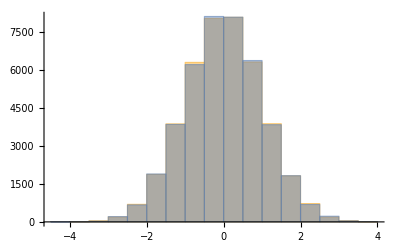

```mathematica
Histogram[{muFinal[[All,1]],RandomVariate[NormalDistribution[0,1],{Length@muFinal}]}]
```

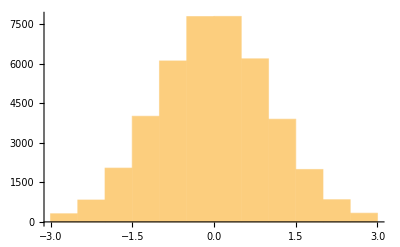

```mathematica
Histogram[muFinal[[All,2]]]
```

```mathematica
qTest=ParallelTable[RandomVariate[NormalDistribution[muFinal[[All,2]][[i]],sigma],{1}][[1]],{i,1,Length@muFinal[[All,2]],1}];
```

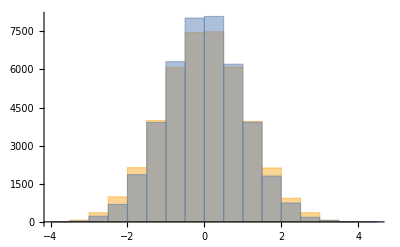

```mathematica
Histogram[{qTest,RandomVariate[NormalDistribution[0,1],{Length@qTest}]}]
```

```mathematica
fGenerate[sigma_,n_Integer]:=Block[{muSamples=RandomVariate[UniformDistribution[{-3,3}],n],q,data,dens,pfprior,ratio,lnormrat,muKept,muFinal,qTest},
q=ParallelTable[RandomVariate[NormalDistribution[muSamples[[i]],sigma],{1}][[1]],{i,1,Length@muSamples,1}];
data=ParallelTable[PDF[NormalDistribution[0,1],q[[i]]],{i,1,Length@q,1}];dens=SmoothKernelDistribution[q];
pfprior=ParallelTable[PDF[dens,q[[i]]],{i,1,Length@q,1}];ratio=data/pfprior;
lnormrat=ratio/Max[ratio];muKept=Table[If[lnormrat[[i]]>RandomReal[],{q[[i]],muSamples[[i]]},-1],{i,1,Length@lnormrat}];muFinal=DeleteCases[muKept,-1];qTest=ParallelTable[RandomVariate[NormalDistribution[muFinal[[All,2]][[i]],sigma],{1}][[1]],{i,1,Length@muFinal[[All,2]],1}];Thread[{muFinal[[All,1]],muFinal[[All,2]],qTest}]]
```

```mathematica
n=100000;
test=fGenerate[0.4,n];
```

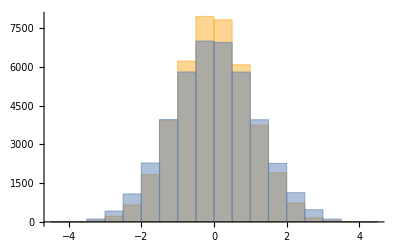

```mathematica
Histogram[{RandomVariate[NormalDistribution[],Length@test[[All,3]]],test[[All,3]]}]
```

```mathematica
sigma={0.001,0.1,0.2,0.3,0.4,0.5,0.6};
```

```mathematica
test=Table[fGenerate[sigma[[i]],n],{i,1,Length@sigma,1}];
```

```mathematica
(1/10)^2+(99/100)
```

1

```mathematica
fSolve[a_]:=Block[{b},Reduce[{b>0,a^2+b^2==1},b][[2]]]
```

```mathematica
fSolve[0.6]
```

0.8

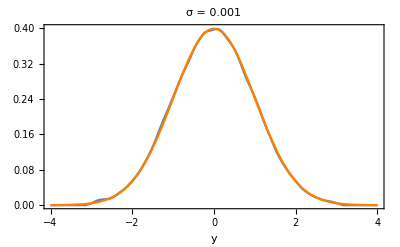
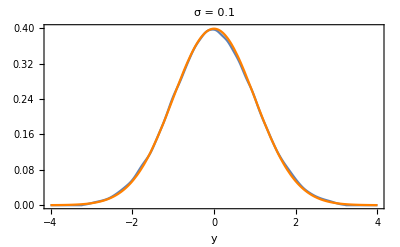
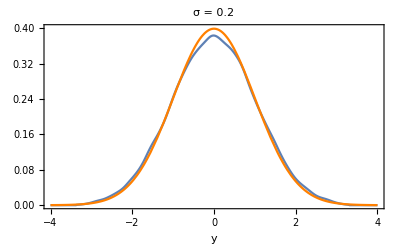
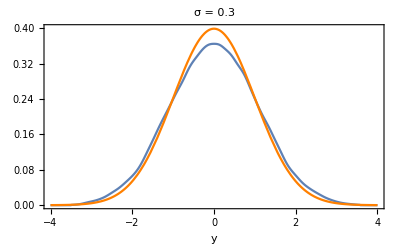
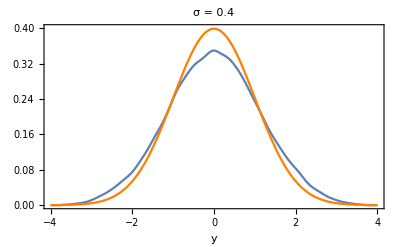
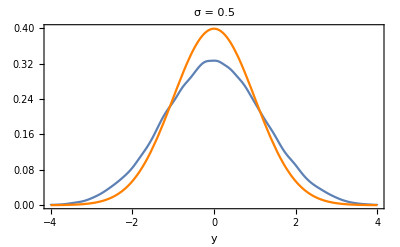

```mathematica
lplots=Table[Show[SmoothHistogram[test[[i]][[All,3]],PlotRange->{{-4,4},{0,0.4}},PlotLabel->StringJoin["σ = ",ToString@sigma[[i]]],LabelStyle->{FontSize->16,Black},Frame->{True,True,False,False},FrameLabel->{"y",""},Axes->False],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->Orange]],{i,1,Length@sigma-1,1}]
```

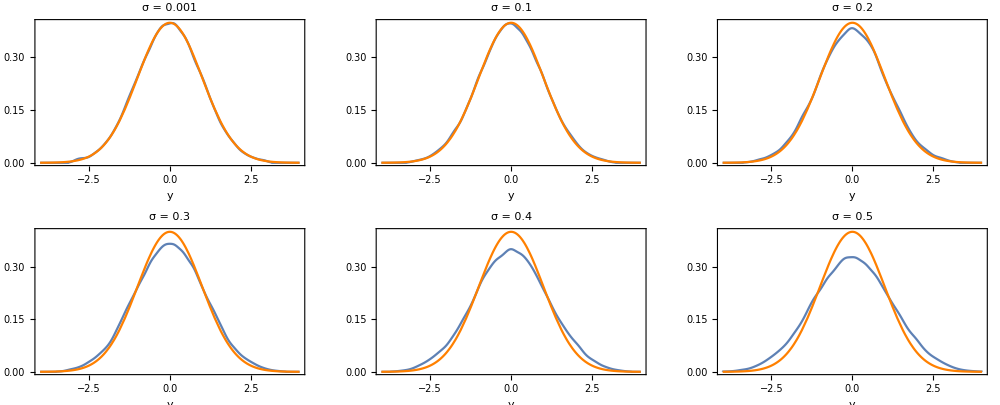

```mathematica
gFinal=GraphicsGrid[{lplots[[1;;3]],lplots[[4;;6]]},ImageSize->1000]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["../figures/stochastic/butler_toy_gaussian.pdf",gFinal]
```

../figures/stochastic/butler_toy_gaussian.pdf

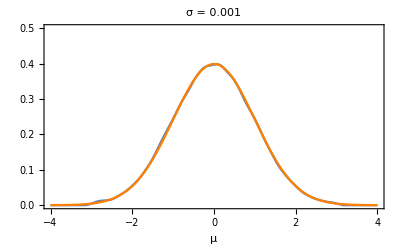
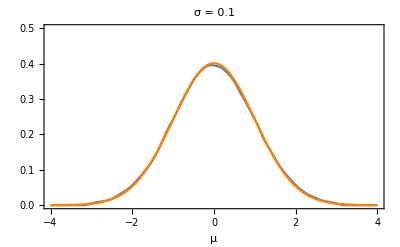
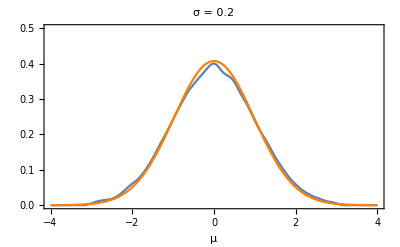
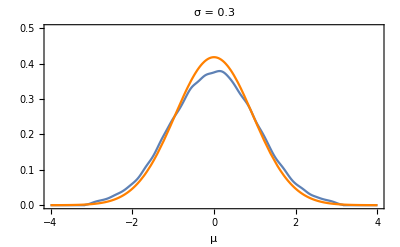
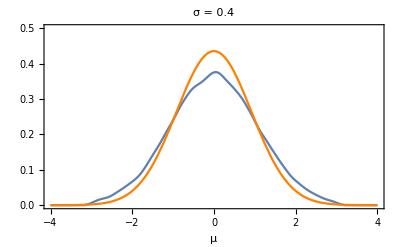
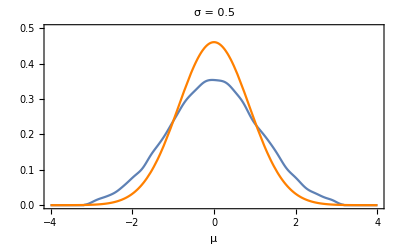

```mathematica
lplots=Table[Show[SmoothHistogram[test[[i]][[All,2]],PlotRange->{{-4,4},{0,0.5}},PlotLabel->StringJoin["σ = ",ToString@sigma[[i]]],LabelStyle->{FontSize->16,Black},Frame->{True,True,False,False},FrameLabel->{"μ",""},Axes->False],Plot[PDF[NormalDistribution[0,fSolve[sigma[[i]]]],x],{x,-4,4},PlotStyle->Orange]],{i,1,Length@sigma-1,1}]
```

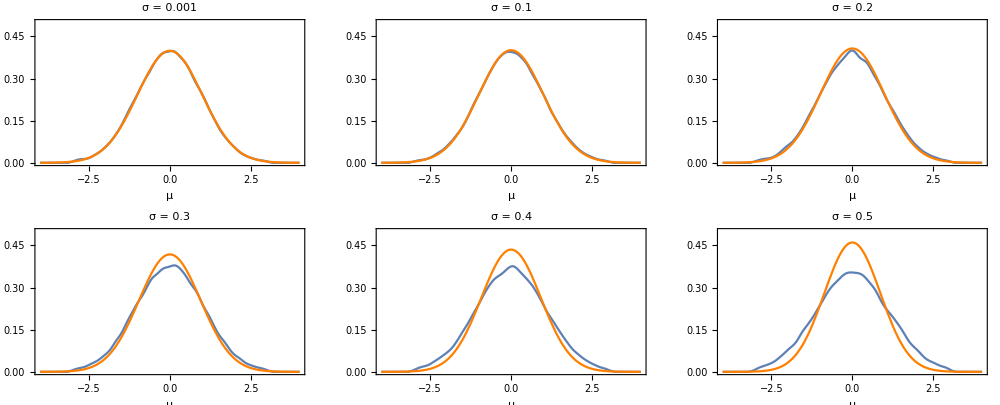

```mathematica
gFinal=GraphicsGrid[{lplots[[1;;3]],lplots[[4;;6]]},ImageSize->1000]
```

```mathematica
Export["../figures/stochastic/butler_toy_gaussian_mu.pdf",gFinal]
```

../figures/stochastic/butler_toy_gaussian_mu.pdf